```mathematica
(* Parameters *)
mmax=7;
LS=2;
LS2=LS^2;
m0=0;
(* Free propagators *)
D0=Table[Simplify[4 Sin[(π p)/LS]^2+m0],{p,0,LS-1}];
G0=Table[Simplify[1/(λ+D0[[p+1]])],{p,0,LS-1}];
G02 = Table[If[Mod[p+q,LS]==0,G0[[p+1]],0],{p,0,LS-1},{q,0,LS-1}];
(* Creating the table of the expansion coefficients *)
G=Table[Table[Table[NULL,{P,1,LS^(2 n)}],{n,1,mmax-m+1}],{m,0,mmax}]; (* TODO: reduce space by momentum conservation constraint *)
(* Recursive calculation of G *)
For[m=0,m≤mmax,m++,
Print["m = ",m];
For[n=1,n≤mmax-m+1,n++,
For[P=0,P<LS^(2n),P++,
ps=Reverse[IntegerDigits[P,LS,2 n]];
PT=Mod[Total[ps],LS];MomentumConservedFlag=(PT==0); (* Testing whether momentum is conserved *)
(* c1 is the First contribution - contact terms *)
c1=0; c2=0; c3=0;
If[n>1,
P1=Quotient[P,LS^2];
c1 += 1/LS G02[[ ps[[1]]+1,ps[[2]]+1 ]] G[[ m+1]][[n-1]][[ P1+1]];
P1= ps[[2n-1]]+LS Mod[Quotient[P,LS],LS^(2n-3)];
c1+= 1/LS G02[[ ps[[1]]+1,ps[[2n]]+1 ]] G[[ m+1]][[n-1]][[P1+1]];
For[A=2,A<=n-1,A++,
P1=ps[[2A-1]]+LS Quotient[Mod[P,LS^(2A-2)],LS];
P2=Quotient[P,LS^(2A)];
c11=Sum[G[[m1+1]][[A-1]][[P1+1]] G[[m-m1+1]][[n-A]][[P2+1]],{m1,0,m}];
c1+= 1/LS G02[[ ps[[1]]+1, ps[[2 A]]+1 ]] c11;
];
,
If[m==0,c1+=1/LS G02[[ ps[[1]]+1,ps[[2]]+1 ]]];
(* End of If[n>1]*) ];
If[ m>0,
(* c2 is the second contribution  - double-trace vertex *)
For[A=2,A≤n,A++,
P1=Mod[P,LS^(2A-2)]; (* This is now the sequence {Subscript[p, 1], Subscript[q, 1], ..., Subscript[p, A-1],Subscript[q, A-1]} *)
P2=Quotient[P,LS^(2A-2)]; (* This is now the sequence {Subscript[p, A], Subscript[q, A], ..., Subscript[p, n],Subscript[q, n]} *)
For[p1t=0,p1t<LS,p1t++,
pAt=Mod[ps[[1]]+ps[[2A-1]]+(LS-p1t),LS];
sP1=p1t + LS Quotient[P1,LS];(* This is now the sequence {Subscript[p, 1] t, Subscript[q, 1], ..., Subscript[p, A-1],Subscript[q, A-1]} *)
sP2=pAt + LS Quotient[P2,LS];(* This is now the sequence {Subscript[p, A] t, Subscript[q, A], ..., Subscript[p, n],Subscript[q, n]} *)
c2 += Sum[G[[m1+1]][[A-1]][[sP1+1]] G[[(m-m1-1)+1]][[n-A+1]][[sP2+1]],{m1,0,m-1}];
];
];
c2*=1/LS G0[[ ps[[1]]+1 ]];
(* c3 is the third contribution - fourth-order vertex *)
P1=LS^3 Quotient[P,LS];
For[p1t=0,p1t<LS,p1t++,
For[q1t=0,q1t<LS,q1t++,
p2t=Mod[ps[[1]]+(LS-p1t)+(LS-q1t),LS];
sP1=p1t + q1t LS +p2t LS^2+P1;
c3 +=D0[[q1t+1]] G[[(m-1)+1]][[n+1]][[sP1+1]];
];
];
c3*=G0[[ ps[[1]]+1 ]];
(* End of If[m>0,...] *) ];
(* Summing up all the contributions *)
c1=Simplify[c1];c2=Simplify[c2];c3= Simplify[c3];
G[[m+1]][[n]][[P+1]]=FullSimplify[c1-c2+c3];
];
];
];
```

m = 0

m = 1

m = 2

m = 3

m = 4

m = 5

m = 6

m = 7

{0.666667,1.03704,1.28395,1.40741,1.37952,1.16674}

{0.333333,0.62963,0.864198,1.01235,1.04298,0.922878}

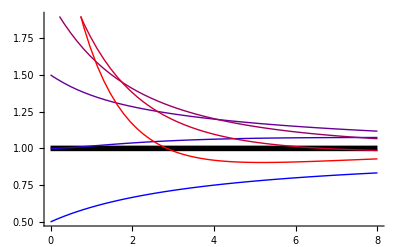

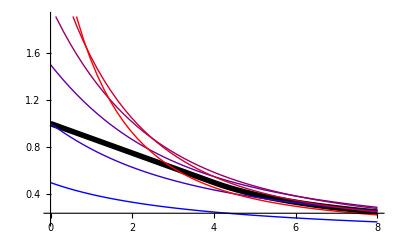

At λ = 0, G00 = {0.5,1.,1.5,2.,2.5,3.}, G01 = {0.5,1.,1.5,2.,2.5,3.} , should be 1.

{{1.,0.5},{0.5,1.},{0.333333,1.5},{0.25,2.},{0.2,2.5},{0.166667,3.}}

{{1.,0.5},{0.5,1.},{0.333333,1.5},{0.25,2.},{0.2,2.5},{0.166667,3.}}

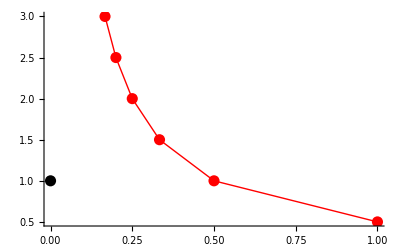

-Graphics-

At λ = 2, G00 = {0.667,1.04,1.28,1.41,1.38,1.17}, G01 = {0.333,0.63,0.864,1.01,1.04,0.923} , should be 0.75

{{1.,0.666667},{0.5,1.03704},{0.333333,1.28395},{0.25,1.40741},{0.2,1.37952},{0.166667,1.16674}}

{{1.,0.333333},{0.5,0.62963},{0.333333,0.864198},{0.25,1.01235},{0.2,1.04298},{0.166667,0.922878}}

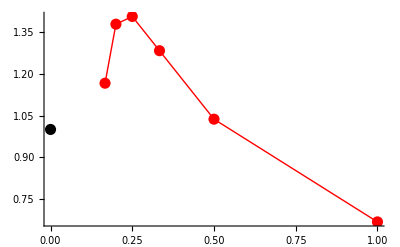

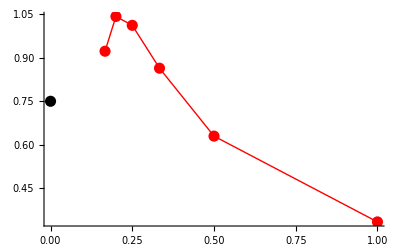

At λ = 4, G00 = {0.75,1.06,1.2,1.2,1.1,0.919}, G01 = {0.25,0.438,0.551,0.587,0.55,0.459} , should be 0.5

{{1.,0.75},{0.5,1.0625},{0.333333,1.19922},{0.25,1.20215},{0.2,1.09607},{0.166667,0.919464}}

{{1.,0.25},{0.5,0.4375},{0.333333,0.550781},{0.25,0.586914},{0.2,0.550415},{0.166667,0.45871}}

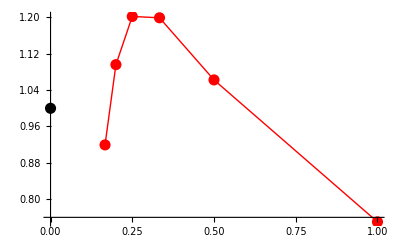

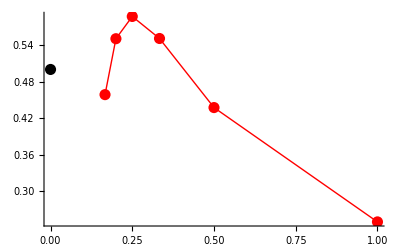

At λ = 8, G00 = {0.833,1.07,1.12,1.07,0.986,0.929}, G01 = {0.167,0.259,0.29,0.28,0.251,0.226} , should be 0.25

{{1.,0.833333},{0.5,1.07407},{0.333333,1.11728},{0.25,1.06584},{0.2,0.986054},{0.166667,0.928669}}

{{1.,0.166667},{0.5,0.259259},{0.333333,0.290123},{0.25,0.279835},{0.2,0.251257},{0.166667,0.22588}}

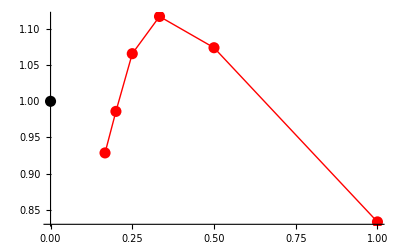

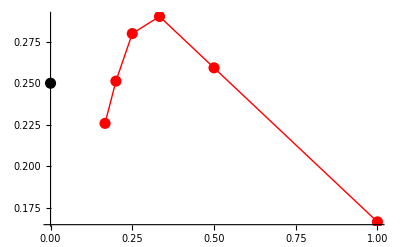

At λ = 16, G00 = {0.9,1.06,1.05,1.01,0.982,0.981}, G01 = {0.1,0.136,0.138,0.129,0.121,0.12} , should be 0.125

{{1.,0.9},{0.5,1.064},{0.333333,1.05424},{0.25,1.00933},{0.2,0.981695},{0.166667,0.981212}}

{{1.,0.1},{0.5,0.136},{0.333333,0.13776},{0.25,0.128589},{0.2,0.121498},{0.166667,0.120437}}

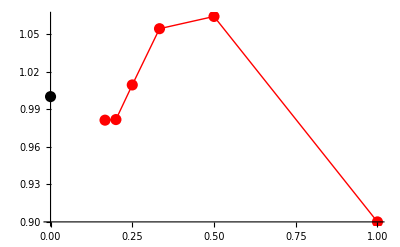

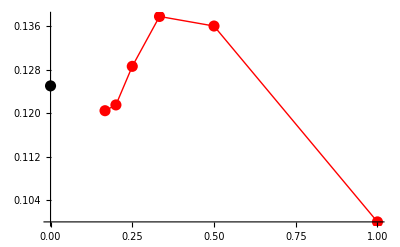

At λ = 32, G00 = {0.944,1.04,1.02,0.998,0.994,0.998}, G01 = {0.0556,0.0672,0.0652,0.0624,0.0617,0.0622} , should be 0.0625

{{1.,0.944444},{0.5,1.0439},{0.333333,1.01989},{0.25,0.997804},{0.2,0.993839},{0.166667,0.997962}}

{{1.,0.0555556},{0.5,0.0672154},{0.333333,0.0651578},{0.25,0.0624002},{0.2,0.0617227},{0.166667,0.0621861}}

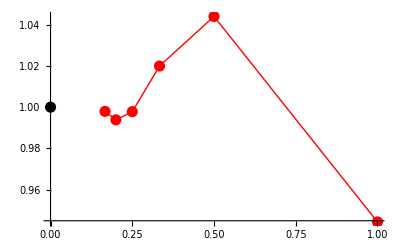

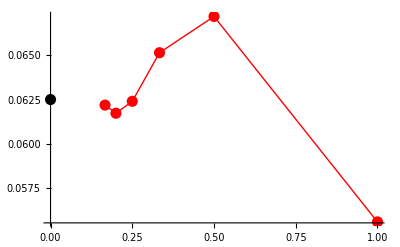

At λ = ∞, G00 = {1.,1.,1.,1.,1.,1.}, G01 = {0,0,0,0,0,0} , should be 0

{{1.,1.},{0.5,1.},{0.333333,1.},{0.25,1.},{0.2,1.},{0.166667,1.}}

{{1.,0.},{0.5,0.},{0.333333,0.},{0.25,0.},{0.2,0.},{0.166667,0.}}

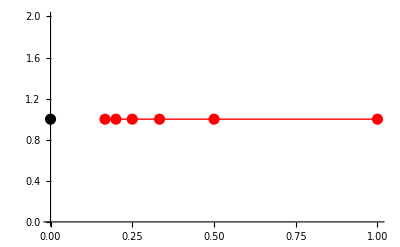

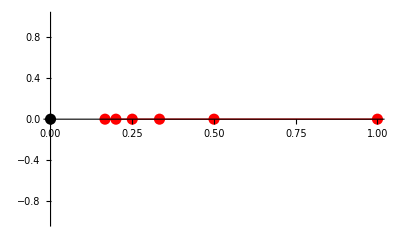

```mathematica
(* Collecting the final expression for the Fourier-transformed G2 *)
G00={}; G01={};
For[mmax1=0,mmax1≤mmax,mmax1++,
G2P=Table[
Sum[λ^(m+1)G[[m+1]][[1]][[(p + LS p)+1]],{m,0,mmax1}],
{p,0,LS-1}];
(* Now the final results for the unitarity norm and the mean link *)
AppendTo[G00,FullSimplify[Total[G2P]]];
AppendTo[G01,FullSimplify[Sum[G2P[[p+1]] Cos[(2π p)/LS],{p,0,LS-1}]]];
];
λ0=2.0;
Print[G00/.{λ->λ0}];
Print[G01/.{λ->λ0}];
G01Exact=If[λ<4,1-λ/8,2/λ];
GrG00={Plot[1,{λ,0,8},PlotStyle->{Black,Thickness[0.01]}]};
GrG01={Plot[G01Exact,{λ,0,8},PlotStyle->{Black,Thickness[0.01]}]};
PlotStyles=Table[RGBColor[m/mmax,0,1-m/mmax],{m,0,mmax}];
AppendTo[GrG00,Plot[G00,{λ,0,8},PlotStyle->PlotStyles]];
AppendTo[GrG01,Plot[G01,{λ,0,8},PlotStyle->PlotStyles]];
Show[GrG00,PlotRange->{0.0,Automatic}]
Show[GrG01,PlotRange->{0.0,Automatic}]
λs={0,2,4,8,16,32,+∞};
For[iλ=1,iλ≤Length[λs],iλ++,
G00T=Limit[G00,λ->λs[[iλ]]];
G01T=Limit[G01,λ->λs[[iλ]]];
G01E=Limit[G01Exact,λ->λs[[iλ]] ];
Print["At λ = ",λs[[iλ]],", G00 = ",N[G00T,3],", G01 = ",N[G01T,3]," , should be ",N[G01E,3] ];
(* Convergence plots *)
G00T2Plot=N[Transpose[{Table[1/(m+1),{m,0,mmax}],G00T}]];
G01T2Plot=N[Transpose[{Table[1/(m+1),{m,0,mmax}],G01T}]];
Print[G00T2Plot];
Print[G01T2Plot];
GrG00=Table[ListPlot[G00T2Plot,PlotRange->All,Joined->(J0==0),PlotStyle->{Red,PointSize[0.02]},PlotRange->{Automatic,{0.0,Automatic}},AxesOrigin->{0,Automatic}],{J0,0,1}];
GrG01=Table[ListPlot[G01T2Plot,PlotRange->All,Joined->(J0==0),PlotStyle->{Red,PointSize[0.02]},PlotRange->{Automatic,{0.0,Automatic}},AxesOrigin->{0,Automatic}],{J0,0,1}];
AppendTo[GrG00,Graphics[{PointSize[0.02],Black,Point[{0.0,1.0}]}]];
AppendTo[GrG01,Graphics[{PointSize[0.02],Black,Point[{0.0,G01E}]}]];
Print[Show[GrG00,PlotRange->All]];
Print[Show[GrG01]];
];
```

```mathematica
For[mmax=1,mmax≤Length[G01],mmax++,
Print[Expand[(4+λ)^(2mmax+1)G01[[mmax]] ]];
];
```

32+16 λ+2 λ^2

1024+1024 λ+352 λ^2+48 λ^3+2 λ^4

24576+35840 λ+20864 λ^2+5888 λ^3+824 λ^4+56 λ^5+2 λ^6

524288+983040 λ+786432 λ^2+343040 λ^3+84864 λ^4+12032 λ^5+1080 λ^6+72 λ^7+2 λ^8

10485760+23330816 λ+23035904 λ^2+13189120 λ^3+4756480 λ^4+1077760 λ^5+158656 λ^6+18304 λ^7+1760 λ^8+88 λ^9+2 λ^10

201326592+494927872 λ+553648128 λ^2+374603776 λ^3+171212800 λ^4+55099392 λ^5+12278784 λ^6+2041344 λ^7+309056 λ^8+37504 λ^9+2496 λ^10+104 λ^11+2 λ^12